# Lecture 5 - exercises

Q1: Write the expression f(x)= x e^-x + x (1 - x), and evaluate it at the points x=0, 0.1, 0.2, 0.4, 0.8.

```mathematica
f[x_]:=x Exp[-x]+x (1-x)
f[0]
f[0.1]
f[0.2]
f[0.4]
f[0.8]
```

0

0.180484

0.323746

0.508128

0.519463

Q2: Find the first three roots of the Bessel function J_1(x). Hint: The Bessel function in Mathematica is BesselJ[n, x]. It may also be useful to plot the function.

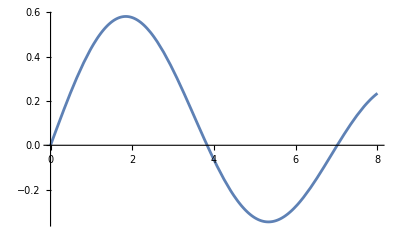

```mathematica
Plot[BesselJ[1,x],{x,-0,8}]
```

```mathematica
NSolve[BesselJ[1,x]==0 && 0<=x<8, x]
```

{{x→0.},{x→3.83171},{x→7.01559}}

Alternative (but FindRoot only takes one guess (?))

```mathematica
FindRoot[BesselJ[1,x]==0,{x,-1,1}]
FindRoot[BesselJ[1,x]==0,{x,-3,4}]
FindRoot[BesselJ[1,x]==0,{x,6.5,7.5}]
```

{x→0.}

{x→3.83171}

{x→7.01559}